```mathematica
Get["path-integrals.m"];
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
haywardNe500 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[2]],{j,1,5}]);Clear[pints];
```

```mathematica
Get["path-integrals-vary-ne.m"];
haywardNe1000 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[1]],{j,1,5}]);
haywardNe250 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[2]],{j,1,5}]);
haywardNe200 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[3]],{j,1,5}]);
Clear[pints];
```

```mathematica
fitVar = 1;
jumpSize = 1;
sigCutoff = 0.99;
start= 0.1;
genVar = 0.001;
```

```mathematica
(************************)
(******* Ne = 1000 *******)
(************************)
```

```mathematica
Clear[time];
time = 0.05;
Clear[selectedNe];
selectedNe = 1000;
```

```mathematica
Do[Clear[neutAUC, pNeutFix,tmp,thresh,Ψ, totalP, Pdetected];
Print[selectedNe, " xxxx ",time":"];
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}];
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
If[Length[thresh] != 1,Throw[{selectedNe,, " xxxx ", start,":"}]];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
Print[pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]];
totalP = NIntegrate[Evaluate[haywardNe1000/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}];
Pdetected = NIntegrate[Evaluate[haywardNe1000/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
Export[StringJoin["pDetection_","Ne",ToString[selectedNe], "_selCoef",ToString[selCoef],".csv"], {{selCoef,selectedNe,time, start,Ψ,totalP,Pdetected}}, "csv"],
{selCoef, {0, 0.0005,0.001,0.005, 0.01}}
]
```

1000 xxxx 0.025 :

0.900446

1.

$Aborted

```mathematica
(***********************)
(******* Ne = 500 *******)
(***********************)
```

```mathematica
Clear[selectedNe];
Clear[time];
time = 0.1;
selectedNe = 500;
Do[Clear[neutAUC, pNeutFix,tmp,thresh,Ψ, totalP, Pdetected];
Print[selectedNe, " xxxx ",time":"];
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}];
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
If[Length[thresh] != 1,Throw[{selectedNe,, " xxxx ", start,":"}]];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
Print[pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]];
totalP = NIntegrate[Evaluate[haywardNe500/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}];
Pdetected = NIntegrate[Evaluate[haywardNe500/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
Export[StringJoin["pDetection_","Ne",ToString[selectedNe], "_selCoef",ToString[selCoef],".csv"], {{selCoef,selectedNe,time, start,Ψ,totalP,Pdetected}}, "csv"],
{selCoef, {0, 0.0005,0.001,0.005, 0.01}}
]
```

```mathematica
(***********************)
(******* Ne = 250 *******)
(***********************)
```

```mathematica
Clear[time];
time = 0.2;
Clear[selectedNe];
selectedNe = 250;
Do[Clear[neutAUC, pNeutFix,tmp,thresh,Ψ, totalP, Pdetected];
Print[selectedNe, " xxxx ",time":"];
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}];
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
If[Length[thresh] != 1,Throw[{selectedNe,, " xxxx ", start,":"}]];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
Print[pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]];
totalP = NIntegrate[Evaluate[haywardNe250/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}];
Pdetected = NIntegrate[Evaluate[haywardNe250/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
Export[StringJoin["pDetection_","Ne",ToString[selectedNe], "_selCoef",ToString[selCoef],".csv"], {{selCoef,selectedNe,time, start,Ψ,totalP,Pdetected}}, "csv"],
{selCoef, {0, 0.0005,0.001,0.005, 0.01}}
]
```

```mathematica
(***********************)
(******* Ne = 200 *******)
(***********************)
```

```mathematica
Clear[time];
time = 0.25;
Clear[selectedNe];
selectedNe = 200;
Do[Clear[neutAUC, pNeutFix,tmp,thresh,Ψ, totalP, Pdetected];
Print[selectedNe, " xxxx ",selCoef":"];
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}];
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
If[Length[thresh] != 1,Throw[{selectedNe,, " xxxx ", start,":"}]];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
Print[pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]];
totalP = NIntegrate[Evaluate[haywardNe200/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}];
Pdetected = NIntegrate[Evaluate[haywardNe200/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
Export[StringJoin["pDetection_","Ne",ToString[selectedNe], "_selCoef",ToString[selCoef],".csv"], {{selCoef,selectedNe,time, start,Ψ,totalP,Pdetected}}, "csv"],
{selCoef, {0, 0.0005,0.001,0.005, 0.01}}
]
```

200 xxxx 0

0.486736

0.99

0.57857 xxxx 0.01

200 xxxx 0.0005 :

0.486736

0.99

0.586705 xxxx 0.0111386

200 xxxx 0.001 :

0.486736

0.99

0.594799 xxxx 0.0123875

200 xxxx 0.005 :

0.486736

0.99

0.657653 xxxx 0.0274263

200 xxxx 0.01 :

0.486736

0.99

0.729651 xxxx 0.0646563

```mathematica
(*****************************************************************)
```

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
```

```mathematica
Get["path-integrals-vary-ne.m"];
haywardNe1000[0] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50]);
For[k = 1, k ≤5,k++,haywardNe1000[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[1]],{j,1,k}]);
]
```

```mathematica
Clear[Pints]
```

```mathematica
fitVar = 1;
jumpSize = 1;
start= 0.1;
genVar = 0.001;
```

```mathematica
Clear[time];
time = 0.05;
Clear[selectedNe];
selectedNe = 1000;
```

```mathematica
selCoef = 0.01;
```

```mathematica
soln = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

{{f→InterpolatingFunction[{{0., 1.}, {0., 0.25}}, <>]}}

```mathematica
pintAUC = NIntegrate[Evaluate[haywardNe1000[5]/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar}],{y,0,1}]
```

0.998505

```mathematica
numAUC = NIntegrate[Evaluate[{f[y, time]} /. soln],{y,0,1}][[1]][[1]]
```

0.99835

```mathematica
(0.998505420766077 - 0.9983496266320906) / 0.9983496266320906
```

0.000156052

```mathematica
funcs  = Append[Evaluate[Table[haywardNe1000[k]/. {x->start,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> time, α ->selCoef, VG->genVar},{k,0,5}]],
Evaluate[f[y,t] /.soln /. {t->time}]];
plt = Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotRange->{{0,1},{-10,10}}]
```

-Graphics-

```mathematica
(*********************************************)
```

```mathematica
Clear[time];
time = 0.025;
Clear[selectedNe];
selectedNe = 1000;
```

```mathematica
selCoef = 0.01;
```

```mathematica
soln = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

{{f→InterpolatingFunction[{{0., 1.}, {0., 0.25}}, <>]}}

```mathematica
pintAUC = NIntegrate[Evaluate[haywardNe1000[5]/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar}],{y,0,1}]
```

0.998653

```mathematica
numAUC = NIntegrate[Evaluate[{f[y, time]} /. soln],{y,0,1}][[1]][[1]]
```

0.999971

```mathematica
(pintAUC - numAUC) / numAUC
```

-0.00131785

```mathematica
funcs  = Append[Evaluate[Table[haywardNe1000[k]/. {x->start,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> time, α ->selCoef, VG->genVar},{k,0,5}]],
Evaluate[f[y,t] /.soln /. {t->time}]];
plt = Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotRange->{{0,1},{-10,10}}]
```

-Graphics-

```mathematica
sigCutoff = 0.99
```

0.99

```mathematica
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}]
pNeutFix = 1- neutAUC
```

0.999756

0.000244337

```mathematica
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}]
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals]
```

-718848.-8.21392 Ψ+26.8728 Ψ^2+448.478 Ψ^3-3924.56 Ψ^4-6365.74 Ψ^5+227984. Ψ^6-905228. Ψ^7-3.80786×10^6 Ψ^8+4.90779×10^7 Ψ^9-1.41322×10^8 Ψ^10-5.31462×10^8 Ψ^11+5.81723×10^9 Ψ^12-1.76422×10^10 Ψ^13-2.05882×10^10 Ψ^14+3.81858×10^11 Ψ^15-1.44149×10^12 Ψ^16+1.37483×10^12 Ψ^17+1.12868×10^13 Ψ^18-6.26319×10^13 Ψ^19+1.45721×10^14 Ψ^20-1.68245×10^13 Ψ^21-1.13718×10^15 Ψ^22+4.41528×10^15 Ψ^23-8.27977×10^15 Ψ^24+1.29625×10^15 Ψ^25+4.38904×10^16 Ψ^26-1.51722×10^17 Ψ^27+2.58981×10^17 Ψ^28-4.35761×10^16 Ψ^29-1.25559×10^18 Ψ^30+4.8055×10^18 Ψ^31-1.16783×10^19 Ψ^32+2.19016×10^19 Ψ^33-3.36101×10^19 Ψ^34+4.31746×10^19 Ψ^35-4.67394×10^19 Ψ^36+4.24507×10^19 Ψ^37-3.17735×10^19 Ψ^38+1.87504×10^19 Ψ^39-7.66435×10^18 Ψ^40+8.62907×10^17 Ψ^41+1.79826×10^18 Ψ^42-1.93215×10^18 Ψ^43+1.19923×10^18 Ψ^44-5.34702×10^17 Ψ^45+1.78031×10^17 Ψ^46-4.37427×10^16 Ψ^47+7.55166×10^15 Ψ^48-8.21993×10^14 Ψ^49+4.2579×10^13 Ψ^50

{{Ψ→0.900446}}

```mathematica
Clear[tmp, thresh]
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0, start+Ψ}]
thresh = Solve[tmp == sigCutoff && 0<Ψ<1, {Ψ}, Reals]
```

0.542231+8.21392 Ψ-26.8728 Ψ^2-448.478 Ψ^3+3924.56 Ψ^4+6365.74 Ψ^5-227984. Ψ^6+905228. Ψ^7+3.80786×10^6 Ψ^8-4.90779×10^7 Ψ^9+1.41322×10^8 Ψ^10+5.31462×10^8 Ψ^11-5.81723×10^9 Ψ^12+1.76422×10^10 Ψ^13+2.05882×10^10 Ψ^14-3.81858×10^11 Ψ^15+1.44149×10^12 Ψ^16-1.37483×10^12 Ψ^17-1.12868×10^13 Ψ^18+6.26319×10^13 Ψ^19-1.45721×10^14 Ψ^20+1.68245×10^13 Ψ^21+1.13718×10^15 Ψ^22-4.41528×10^15 Ψ^23+8.27977×10^15 Ψ^24-1.29625×10^15 Ψ^25-4.38904×10^16 Ψ^26+1.51722×10^17 Ψ^27-2.58981×10^17 Ψ^28+4.35761×10^16 Ψ^29+1.25559×10^18 Ψ^30-4.8055×10^18 Ψ^31+1.16783×10^19 Ψ^32-2.19016×10^19 Ψ^33+3.36101×10^19 Ψ^34-4.31746×10^19 Ψ^35+4.67394×10^19 Ψ^36-4.24507×10^19 Ψ^37+3.17735×10^19 Ψ^38-1.87504×10^19 Ψ^39+7.66435×10^18 Ψ^40-8.62907×10^17 Ψ^41-1.79826×10^18 Ψ^42+1.93215×10^18 Ψ^43-1.19923×10^18 Ψ^44+5.34702×10^17 Ψ^45-1.78031×10^17 Ψ^46+4.37427×10^16 Ψ^47-7.55166×10^15 Ψ^48+8.21993×10^14 Ψ^49-4.2579×10^13 Ψ^50

{{Ψ→0.130201},{Ψ→0.462831}}

```mathematica
If[Length[thresh] != 1,Throw[{selectedNe, " xxxx ", start,":"}]]
```

Throw::nocatch: Uncaught Throw[{1000, xxxx ,0.1,:}] returned to top level.

Hold[Throw[{1000, xxxx ,0.1,:}]]

```mathematica
Ψ = Ψ /. thresh
Ψ = Ψ[[1]]
Print[Ψ]
Print[pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]]
totalP = NIntegrate[Evaluate[haywardNe1000[5]/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}]
Pdetected = NIntegrate[Evaluate[haywardNe1000[5]/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}]
```

{0.130201,0.462831}

0.130201

0.130201

0.990244

0.998653

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.942855}. NIntegrate obtained 0.109989 and 1.45442×10^-7 for the integral and error estimates.

0.109989

```mathematica
(1-totalP) + NIntegrate[Evaluate[haywardNe1000[5]/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0, start+Ψ}]
```

0.890011

```mathematica
0.10998929287728766 + 0.890011165699323
```

1.

```mathematica
NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y,start+Ψ,1}]
```

0.00975566

```mathematica
Clear[neutAUC, pNeutFix,tmp,thresh,Ψ, totalP, Pdetected]
```

```mathematica
(***********************************************************************)
```

```mathematica
Get["path-integrals-vary-ne.m"];
haywardNe200[0] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50]);
For[k = 1, k ≤5,k++,haywardNe200[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[3]],{j,1,k}]);
]
Clear[pints]
```

```mathematica
Clear[time];
time = 0.25;
Clear[selectedNe];
selectedNe = 200;
```

```mathematica
selCoef = 0.01;
```

```mathematica
soln = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

{{f→InterpolatingFunction[{{0., 1.}, {0., 0.25}}, <>]}}

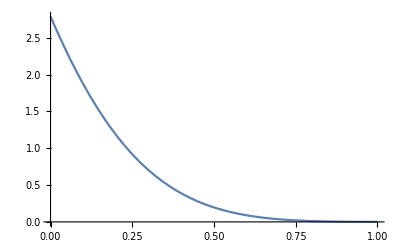

```mathematica
Plot[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}]
```

```mathematica
pintAUC = NIntegrate[Evaluate[haywardNe200[5]/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar}],{y,0,1}]
```

0.729651

```mathematica
numAUC = NIntegrate[Evaluate[{f[y, time]} /. soln],{y,0,1}][[1]][[1]]
```

0.729647

```mathematica
(pintAUC - numAUC) / numAUC
```

5.17463×10^-6

```mathematica
funcs  = Append[Evaluate[Table[haywardNe200[k]/. {x->start,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> time, α ->selCoef, VG->genVar},{k,0,5}]],
Evaluate[f[y,t] /.soln /. {t->time}]];
plt = Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotRange->{{0,1},{-10,10}}]
```

-Graphics-

```mathematica
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}]
pNeutFix = 1- neutAUC
```

0.57857

0.42143

```mathematica
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}]
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals]
```

0.347502-1.8709 Ψ+4.00895 Ψ^2-3.88477 Ψ^3+0.399079 Ψ^4+3.19228 Ψ^5-3.80601 Ψ^6+2.23487 Ψ^7-0.727544 Ψ^8+0.0953537 Ψ^9+0.0215558 Ψ^10-0.0128851 Ψ^11+0.00284419 Ψ^12-0.000344337 Ψ^13+0.0000207 Ψ^14+1.34742×10^-7 Ψ^15-1.25899×10^-7 Ψ^16+1.01897×10^-8 Ψ^17-4.13846×10^-10 Ψ^18+8.39287×10^-12 Ψ^19-1.28791×10^-14 Ψ^20-3.6891×10^-15 Ψ^21+9.55328×10^-17 Ψ^22-1.1756×10^-18 Ψ^23+7.05363×10^-21 Ψ^24-2.4204×10^-24 Ψ^25-2.74849×10^-25 Ψ^26+2.04355×10^-27 Ψ^27-7.18088×10^-30 Ψ^28+1.19608×10^-32 Ψ^29+9.02592×10^-37 Ψ^30-4.48168×10^-38 Ψ^31+9.12708×10^-41 Ψ^32-8.91783×10^-44 Ψ^33+3.98755×10^-47 Ψ^34+3.98864×10^-51 Ψ^35-1.48282×10^-53 Ψ^36+8.1622×10^-57 Ψ^37-2.19303×10^-60 Ψ^38+2.57214×10^-64 Ψ^39+1.52867×10^-68 Ψ^40-9.65799×10^-72 Ψ^41+1.43547×10^-75 Ψ^42-1.0541×10^-79 Ψ^43+3.16669×10^-84 Ψ^44+9.11724×10^-89 Ψ^45-1.22003×10^-92 Ψ^46+5.00037×10^-97 Ψ^47-1.00158×10^-101 Ψ^48+5.86817×10^-107 Ψ^49+1.09892×10^-111 Ψ^50

{{Ψ→0.486736}}

```mathematica
If[Length[thresh] != 1,Throw[{selectedNe,, " xxxx ", start,":"}]]
```

```mathematica
Ψ = Ψ /. thresh
Ψ = Ψ[[1]]
Print[Ψ]
```

{0.486736}

0.486736

0.486736

```mathematica
Print[pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]]
totalP = NIntegrate[Evaluate[haywardNe200[5]/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, 0,1}]
Pdetected = NIntegrate[Evaluate[haywardNe200[5]/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],{y, start+Ψ,1}]
```

0.99

0.729651

0.0646563